```mathematica
y2=(1-α)(y[0]+h/3(f[2]+4f[1]+f[0]))+α(y[1]+h/12(5f[2]+8f[1]-f[0]))
```

(1-α) (1/3 h (f[0]+4 f[1]+f[2])+y[0])+α (1/12 h (-f[0]+8 f[1]+5 f[2])+y[1])

```mathematica
y2c=Collect[y2,{y[_],f[_]}]
```

(1/3 h (1-α)-(h α)/12) f[0]+(4/3 h (1-α)+(2 h α)/3) f[1]+(1/3 h (1-α)+(5 h α)/12) f[2]+(1-α) y[0]+α y[1]

```mathematica
y2c/.{Times[e__,ff:f[_]]:>Simplify[Times[e,ff]]}
```

-1/12 h (-4+5 α) f[0]-2/3 h (-2+α) f[1]+1/12 h (4+α) f[2]+(1-α) y[0]+α y[1]

```mathematica
β0=1/12(-4+5 α) ;
β1=2/3(-2+α);
β2=-1/12 (4+α) ;
```

```mathematica
α0=(1-α)
α1=α 
α2=-1
```

1-α

α

-1

```mathematica
ρ[z_]:=α0+α1 z+α2 z^2
σ[z_]:=β0+β1 z+β2 z^2
zz=Exp[I ξ];
μ=ρ[zz]/σ[zz]
μ/.ξ->π
```

(1-ⅇ^(2 ⅈ ξ)-α+ⅇ^(ⅈ ξ) α)/(1/12 ⅇ^(2 ⅈ ξ) (-4-α)+2/3 ⅇ^(ⅈ ξ) (-2+α)+1/12 (-4+5 α))

-(2 α)/(1/12 (-4-α)-2/3 (-2+α)+1/12 (-4+5 α))

```mathematica
Simplify[-(2 α)/(1/12 (-4-α)-2/3 (-2+α)+1/12 (-4+5 α))]
```

(6 α)/(-2+α)

```mathematica
Manipulate[
ParametricPlot[{Re[μ],Im[μ]}/.α->α0
,{ξ,0,2π}
,MaxRecursion->3
,PlotPoints-> 100
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
,{α0,0,2}
]
```

```mathematica
A={a-1,-a,1,0,0};
B={(4-5*a)/12,(4-2*a)/3,(4+a)/12,0,0};
k=3;p=3;
C111=1/((p+1)!)(∑_(i=0)^k A[[i+1]]*i^(p+1)-(p+1)*∑_(i=0)^k B[[i+1]]*i^p)/(∑_(i=0)^k B[[i+1]])(*C*)
```

(16-a-4 (1/3 (4-2 a)+(2 (4+a))/3))/(24 (1/12 (4-5 a)+1/3 (4-2 a)+(4+a)/12))

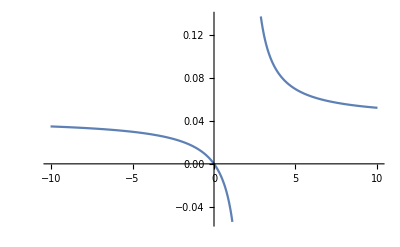

```mathematica
Plot[a/(24 (-2+a)),{a,-10.04,10.04}]
```

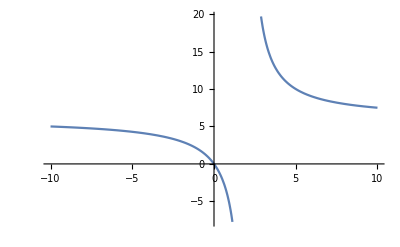

```mathematica
Plot[(6 α)/(-2+α),{α,-10,10}]
```

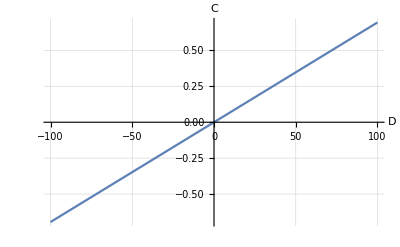

```mathematica
Plot[a/144,{a,-100,100},PlotLabel->None,LabelStyle->{13,GrayLevel[0]},GridLines->Automatic,AxesLabel->{Style[D,Medium],Style[C,Medium]},AxesStyle->{{Arrowheads[0.04],AbsoluteThickness[1]}, {Arrowheads[0.04],AbsoluteThickness[1]}}]
```